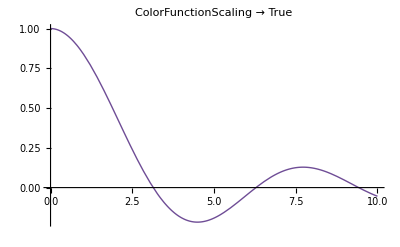

```mathematica
refPlot = Plot[Sinc[x], {x, 0, 10},
PlotStyle -> Thick,
ColorFunction -> Function[{x,y}, ColorData["Rainbow"][y]], 
PlotRange -> All,
PlotLabel -> "ColorFunctionScaling → True"
]
```

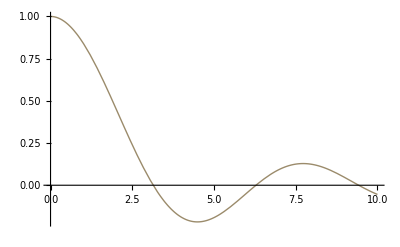

```mathematica
Plot[Sinc[x], {x, 0, 10},
PlotStyle -> Thick,
ColorFunction -> (ColorData["Rainbow"][#1] &), 
PlotRange -> All
]
```

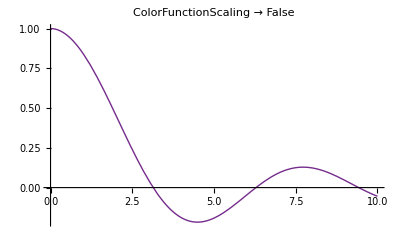

-Graphics-

/home/david/github/ICardiodLise/ColorScalingTrue.jpg

/home/david/github/ICardiodLise/ColorScalingFalse.jpg

```mathematica
falsePlot = Plot[Sinc[x], {x, 0, 10},
PlotStyle -> Thick,
ColorFunction -> Function[{x,y}, ColorData["Rainbow"][y]], 
ColorFunctionScaling -> False,
PlotRange -> All,
PlotLabel -> "ColorFunctionScaling → False"
]

refPlot

Export[
"/home/david/github/ICardiodLise/ColorScalingTrue.jpg", refPlot]

Export[
"/home/david/github/ICardiodLise/ColorScalingFalse.jpg", falsePlot]
```

```mathematica
ColorData["VisibleSpectrum"]
```

ColorDataFunction[…]